#### Definitions

```mathematica
(* Import QuESTlink *)
Import["https://qtechtheory.org/QuESTlink.m"];
CreateDownloadedQuESTEnv[];

(* controlled SWAP operation between two full registers *)
cSWAPregs[reg1_,reg2_,qubitsperReg_,controlQB_]:=Table[
Subscript[C, controlQB][Subscript[SWAP, reg1*qubitsperReg+k,reg2*qubitsperReg+k]],{k,0,qubitsperReg-1}]

(* Derangement circuit for 2 copies *)
D2[qubitsperReg_,observable_]:= With[{controlQB=2*qubitsperReg},
Join[{Subscript[H, controlQB]},cSWAPregs[reg1=0,reg2=1,qubitsperReg,controlQB],
Circuit[Evaluate@observable]/.{Subscript[Id, n_]:>Subscript[Id, n+qubitsperReg],Subscript[O_, n_]:>Subscript[C, controlQB][Subscript[O, n+qubitsperReg]]}
,{Subscript[H, controlQB]}]
]

isValidDerangement[swaps1_,nCopies_]:=With[{cycles=PermutationProduct@@Table[Cycles[{swaps1[[k]]+1}],{k,1,Length@swaps1}]},
(* We check two conditions:
1) the cyclic permutation representation of the swaps is a full n-cycle, where n is the number of copies
	2) the largest index that the permutations act on is identical to the number of copies
 *)
{Dimensions[cycles/.{Cycles[cc_]:>cc}]=={1,nCopies}&&nCopies==Max[swaps1+1],cycles}
];

(* Derangement circuit for n copies *)
Dn[nCopies_,swaps_,qubitsperReg_,observable_]:= With[{controlQB=nCopies*qubitsperReg},
Join[{Subscript[H, controlQB]},
Flatten@Table[cSWAPregs[reg1=swaps[[k,1]],reg2=swaps[[k,2]],qubitsperReg,controlQB],{k,1,Length@swaps}],
Circuit[Evaluate@observable]/.{Subscript[Id, n_]:>Subscript[Id, n+qubitsperReg*(nCopies-1)],Subscript[O_, n_]:>Subscript[C, controlQB][Subscript[O, n+qubitsperReg*(nCopies-1)]]}
,{Subscript[H, controlQB]}]
]

(* Draw derangement circuit with highligting the different registers *)
txt[in_]:=Text[Style[in,FontFamily->"Times New Roman",FontSize->12]]

DrawDerangementCircuit[derangementCirc_,numQs_,numCopies_]:=DrawCircuit[derangementCirc, 
Epilog -> Join[{
	FaceForm[None],EdgeForm[Directive[Red,Dashed]]},
Flatten@Table[
	{Text[Style[StringForm["Reg. ``",k],FontSize->12],{0,k*numQs+.4},{-1,-1}],EdgeForm[Directive[{Red,Blue}[[Mod[k,2]+1]],Dashed,Opacity[0.4]]],
	Rectangle[{0,k*numQs +.2}, {Length[derangementCirc],(k+1)numQs-.2}]},{k,0,numCopies-1}]
	]
]

(* Create n copies of a circuit -- this can be the input of the derangement circuit *)
CopiesOfCircuit[circuit_,numCopies_,qubitsperReg_]:=Flatten@Table[circuit/.{Subscript[gate_, n_]:>Subscript[gate, n+k*qubitsperReg],Subscript[gate_, n1_,n2_]:>Subscript[gate, n1+k*qubitsperReg,n2+k*qubitsperReg]},{k,0,numCopies-1}]
```

URLDownload::invhttp: Failed writing body (0 != 16384).

#### 1) Example of a simple derangement circuit

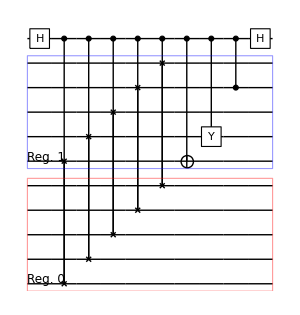

```mathematica
(* number of qubits in a register *)
numQs=5;
(* set observable to be measured *)
observable=Subscript[X, 0] Subscript[Y, 1] Subscript[Z, 3];
(* generate derangement circuit for 2 copies *)
derangementCirc=D2[numQs,observable];
(* Draw derangement circuit and highligt the different registers *)
DrawDerangementCircuit[derangementCirc,numQs,2]
```

#### 2) Mitigate errors in noisy circuits

#### Noisy circuit that generates GHZ states

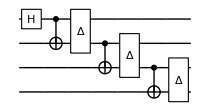
Noisy GHZ circuit:  -Graphics-

```mathematica
numQs=4;
noisyGHZcirc=Join[{Subscript[H, numQs-1]},Flatten@Table[{Subscript[C, n][Subscript[X, n-1]],Subscript[Depol, n,n-1][ϵ]},{n,numQs-1,1,-1}]];
Print["Noisy GHZ circuit: "DrawCircuit[noisyGHZcirc]]

(* set observable with -- known ideal expectation value is 1*)
observable=Product[Subscript[X, k],{k,0,numQs-1}];
idealExpectation=1.;
(* compute expectation value errors for various levels of noise *)
{ρ,ϕ}=CreateDensityQuregs[numQs,2];
errors=Table[
ApplyCircuit[noisyGHZcirc/.{ϵ->10^x},InitZeroState@ρ];
{10^x,Abs[CalcExpecPauliSum[ρ,observable,ϕ]-idealExpectation]}
,{x,-3,-1,0.2}];
DestroyAllQuregs[];
```

#### Setting up derangement circuit for 2 GHZ copies

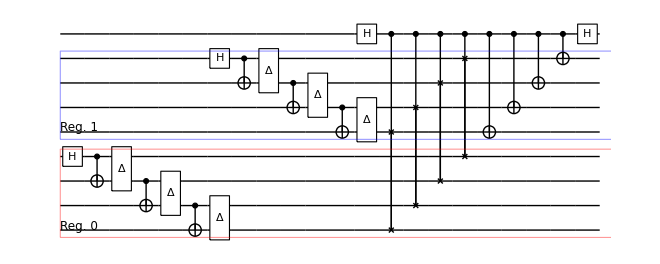
Full derangement circuit takes 2 copies of the GHZ preparation circuits: -Graphics-

```mathematica
(* derangement circuit for 2 copies (identity observable required for correct normalisation) *)
{derangementCirc,derangementCircId}=D2[numQs,#]&/@{observable,Subscript[Id, 0]};
{fullCirc,fullCircId}=Join[CopiesOfCircuit[noisyGHZcirc,2,numQs],#]&/@{derangementCirc,derangementCircId};

Print["Full derangement circuit takes 2 copies of the GHZ preparation circuits: ",
DrawDerangementCircuit[fullCirc,numQs,2]
];
```

#### Compare the mitigated and unmitigated errors

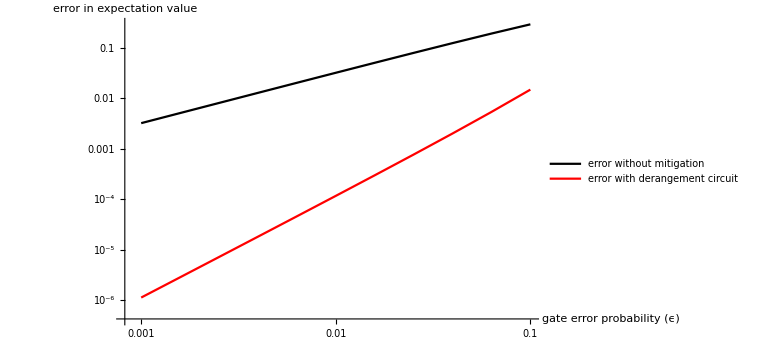
Plotting errors with and without error mitigation:-Graphics-

```mathematica
ρ=CreateDensityQureg[2*numQs+1];
(* compute expectation value errors for various levels of noise *)
errorsWithDerangement=Table[
ApplyCircuit[fullCirc/.{ϵ->10^x},InitZeroState@ρ];
term1=2CalcProbOfOutcome[ρ,2*numQs,0]-1;
ApplyCircuit[fullCircId/.{ϵ->10^x},InitZeroState@ρ];
term2=2CalcProbOfOutcome[ρ,2*numQs,0]-1;
{10^x,Abs[term1/term2-idealExpectation]}
,{x,-3,-1,0.2}];
DestroyAllQuregs[];

plot=ListLogLogPlot[{errors,errorsWithDerangement},
PlotLegends->{txt@"error without mitigation",txt@"error with derangement circuit"},
AxesLabel->{txt@"gate error probability (ϵ)",txt@"error in expectation value"}
,ImageSize->Large,Joined->True,PlotStyle->{Black,Red}
];
Print["Plotting errors with and without error mitigation:", plot];
```

#### 3) General derangement circuits for n copies

#### Checking validity of permutations

```mathematica
(* For more than 2 copies we have a number of different possiblities to implement derangements via different permutations *)
nCopies=4;
numQs=2;
observable=Subscript[X, 0] Subscript[Z, 1];
derangementPatterns={
{{0,1},{0,2},{0,3}}
,
{{0,1},{1,2},{2,3}}
,
{{0,1},{1,2},{1,3}}
};
(* we can check whether the given set of permutations represent a valid derangement operation *)
Print["Validity of derangement ",#, " and its cyclic permutation representation:  ", isValidDerangement[#,nCopies]]&/@derangementPatterns;
```

Validity of derangement {{0,1},{0,2},{0,3}} and its cyclic permutation representation:  {True,Cycles[{{1,2,3,4}}]}

Validity of derangement {{0,1},{1,2},{2,3}} and its cyclic permutation representation:  {True,Cycles[{{1,4,3,2}}]}

Validity of derangement {{0,1},{1,2},{1,3}} and its cyclic permutation representation:  {True,Cycles[{{1,3,4,2}}]}

#### generate random ρ and compute the expectation value Tr[O ρ^n] for reference

```mathematica
rand=With[{r=RandomComplex[{-1-ⅈ,1+ⅈ},{2^numQs,2^numQs}]},
	r . r† / Tr[r . r†]];
{randρ,ϕ}=CreateDensityQuregs[numQs,2];
SetQuregMatrix[randρ,MatrixPower[rand,nCopies]];

Print["expectation value ",StringForm["Tr[O ρ^(``)]",nCopies]," of the observable O is: ",
CalcExpecPauliSum[randρ,observable,ϕ]];
DestroyAllQuregs[];
```

expectation value Tr[O ρ^(RowBox[{)] of the observable O is: -0.0724807

#### Simulate various n-copy derangement circuits

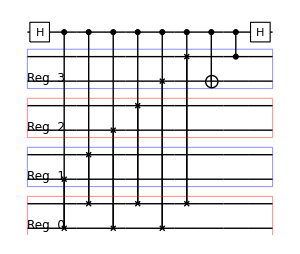
Derangement: {{0,1},{0,2},{0,3}}, expectation value: -0.0724807 via the circuit:
-Graphics-

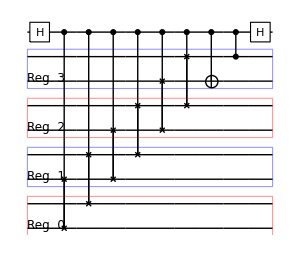
Derangement: {{0,1},{1,2},{2,3}}, expectation value: -0.0724807 via the circuit:
-Graphics-

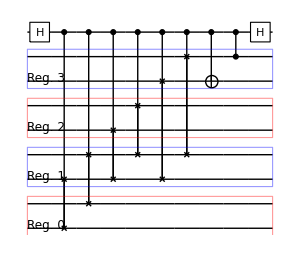
Derangement: {{0,1},{1,2},{1,3}}, expectation value: -0.0724807 via the circuit:
-Graphics-

```mathematica
(* Generate n copies of the random state plus the ancilla qubit *)
randCopies=Module[{kp},
kp=KroneckerProduct[{{1,0},{0,0}},KroneckerProduct[rand,rand]];
Do[kp=KroneckerProduct[kp,rand],nCopies-2];
kp
];
ρ=CreateDensityQureg[nCopies*numQs+1];

Do[
swaps=derangementPatterns[[k]];
derangementCirc=Dn[nCopies,swaps,numQs,observable];
SetQuregMatrix[ρ,randCopies];
ApplyCircuit[derangementCirc,ρ];
Print["Derangement: ",
 swaps,", expectation value: ",2CalcProbOfOutcome[ρ,nCopies*numQs,0]-1,
" via the circuit:\n",
DrawDerangementCircuit[derangementCirc,numQs,nCopies]
];

,{k,1,Length@derangementPatterns}]

DestroyAllQuregs[];
```